# A Boolean model of geroconversion

Loading the library

```mathematica
$Path = $Path  ∪ {NotebookDirectory[]};
```

```mathematica
<<Booned`
```

```mathematica
Clear[Insulin,GF, Senescence, G1S,MAPK, p16,MDM2,p53,p21,AKT,mTORC1S6K1, ATP, IRSPIK3CA, AMPK, PTEN,TSC, MYC, CDK2,RB1, E2F1,PRC, Metabolism,PP2A, FOXO, PP1C]
```

#### Transition function

```mathematica
TF = {
   Insulin -> Insulin,
   GF -> GF,
   Senescence ->  (! p16 && p21 && mTORC1S6K1) || (p16),
   G1S -> (! p21 && CDK2 && E2F1 && Metabolism),
   MAPK -> (GF && ! PP2A),
   p16 -> (MAPK && ! p53 && ! E2F1 && ! PRC),
   MDM2 -> (! p16 && ! p53 && AKT && ! mTORC1S6K1 && ! MYC && ! E2F1) || (! p16 && p53 && ! mTORC1S6K1 && ! MYC && ! E2F1) || (p16 && ! mTORC1S6K1 && ! MYC && ! E2F1),
   p53 -> (! MDM2),
   p21 -> (! p53 && ! AKT && ! MYC && FOXO) || (p53 && ! AKT && ! MYC),
   AKT -> (! IRSPIK3CA && ! PTEN && CDK2 && ! PP2A) || (IRSPIK3CA && ! PTEN && ! PP2A),
   mTORC1S6K1 -> (! AMPK && ! TSC),
   ATP -> Metabolism,
   IRSPIK3CA -> Insulin,
   AMPK -> (p53 && ! ATP),
   PTEN -> (p53 && ! AKT),
   TSC -> (! MAPK && ! AKT && AMPK),
   MYC -> (MAPK && ! p53 && mTORC1S6K1 && E2F1),
   CDK2 -> (! p21 && mTORC1S6K1 && ! MYC && E2F1) || (! p21 && mTORC1S6K1 && MYC),
   RB1 -> (! CDK2),
   E2F1 -> (! GF && MYC && ! RB1 && E2F1) || (GF && ! RB1 && E2F1),
   PRC -> (! AKT && MYC),
   Metabolism -> (! MAPK && ! AKT && mTORC1S6K1 && PP1C) || (! MAPK && AKT && mTORC1S6K1) || (MAPK && ! AKT && PP1C) || (MAPK && AKT),
   PP2A -> (! mTORC1S6K1),
   FOXO -> (! MAPK && ! p16 && ! AKT && ! AMPK && Metabolism) || (! MAPK && ! p16 && ! AKT && AMPK) || (! MAPK && p16 && ! AKT),
   PP1C -> (! MAPK && AKT) || (MAPK)
   };
```

#### List of rules

```mathematica
F = <|
   Insulin -> Insulin,
   GF -> GF,
   Senescence ->  (! p16 && p21 && mTORC1S6K1) || (p16),
   G1S -> (! p21 && CDK2 && E2F1 && Metabolism),
   MAPK -> (GF && ! PP2A),
   p16 -> (MAPK && ! p53 && ! E2F1 && ! PRC),
   MDM2 -> (! p16 && ! p53 && AKT && ! mTORC1S6K1 && ! MYC && ! E2F1) || (! p16 && p53 && ! mTORC1S6K1 && ! MYC && ! E2F1) || (p16 && ! mTORC1S6K1 && ! MYC && ! E2F1),
   p53 -> (! MDM2),
   p21 -> (! p53 && ! AKT && ! MYC && FOXO) || (p53 && ! AKT && ! MYC),
   AKT -> (! IRSPIK3CA && ! PTEN && CDK2 && ! PP2A) || (IRSPIK3CA && ! PTEN && ! PP2A),
   mTORC1S6K1 -> (! AMPK && ! TSC),
   ATP -> Metabolism,
   IRSPIK3CA -> Insulin,
   AMPK -> (p53 && ! ATP),
   PTEN -> (p53 && ! AKT),
   TSC -> (! MAPK && ! AKT && AMPK),
   MYC -> (MAPK && ! p53 && mTORC1S6K1 && E2F1),
   CDK2 -> (! p21 && mTORC1S6K1 && ! MYC && E2F1) || (! p21 && mTORC1S6K1 && MYC),
   RB1 -> (! CDK2),
   E2F1 -> (! GF && MYC && ! RB1 && E2F1) || (GF && ! RB1 && E2F1),
   PRC -> (! AKT && MYC),
   Metabolism -> (! MAPK && ! AKT && mTORC1S6K1 && PP1C) || (! MAPK && AKT && mTORC1S6K1) || (MAPK && ! AKT && PP1C) || (MAPK && AKT),
   PP2A -> (! mTORC1S6K1),
   FOXO -> (! MAPK && ! p16 && ! AKT && ! AMPK && Metabolism) || (! MAPK && ! p16 && ! AKT && AMPK) || (! MAPK && p16 && ! AKT),
   PP1C -> (! MAPK && AKT) || (MAPK)
   |>
```

<|Insulin→Insulin,GF→GF,Senescence→(!p16&&p21&&mTORC1S6K1)||p16,G1S→!p21&&CDK2&&E2F1&&Metabolism,MAPK→GF&&!PP2A,p16→MAPK&&!p53&&!E2F1&&!PRC,MDM2→(!p16&&!p53&&AKT&&!mTORC1S6K1&&!MYC&&!E2F1)||(!p16&&p53&&!mTORC1S6K1&&!MYC&&!E2F1)||(p16&&!mTORC1S6K1&&!MYC&&!E2F1),p53→!MDM2,p21→(!p53&&!AKT&&!MYC&&FOXO)||(p53&&!AKT&&!MYC),AKT→(!IRSPIK3CA&&!PTEN&&CDK2&&!PP2A)||(IRSPIK3CA&&!PTEN&&!PP2A),mTORC1S6K1→!AMPK&&!TSC,ATP→Metabolism,IRSPIK3CA→Insulin,AMPK→p53&&!ATP,PTEN→p53&&!AKT,TSC→!MAPK&&!AKT&&AMPK,MYC→MAPK&&!p53&&mTORC1S6K1&&E2F1,CDK2→(!p21&&mTORC1S6K1&&!MYC&&E2F1)||(!p21&&mTORC1S6K1&&MYC),RB1→!CDK2,E2F1→(!GF&&MYC&&!RB1&&E2F1)||(GF&&!RB1&&E2F1),PRC→!AKT&&MYC,Metabolism→(!MAPK&&!AKT&&mTORC1S6K1&&PP1C)||(!MAPK&&AKT&&mTORC1S6K1)||(MAPK&&!AKT&&PP1C)||(MAPK&&AKT),PP2A→!mTORC1S6K1,FOXO→(!MAPK&&!p16&&!AKT&&!AMPK&&Metabolism)||(!MAPK&&!p16&&!AKT&&AMPK)||(!MAPK&&p16&&!AKT),PP1C→(!MAPK&&AKT)||MAPK|>

```mathematica
Highlighted@TraditionalForm@TableForm[TF]
```

Insulin→Insulin
GF→GF
Senescence→(¬p16∧p21∧mTORC1S6K1)∨p16
G1S→¬p21∧CDK2∧E2F1∧Metabolism
MAPK→GF∧¬PP2A
p16→MAPK∧¬p53∧¬E2F1∧¬PRC
MDM2→(¬p16∧¬p53∧AKT∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(¬p16∧p53∧¬mTORC1S6K1∧¬MYC∧¬E2F1)∨(p16∧¬mTORC1S6K1∧¬MYC∧¬E2F1)
p53→¬MDM2
p21→(¬p53∧¬AKT∧¬MYC∧FOXO)∨(p53∧¬AKT∧¬MYC)
AKT→(¬IRSPIK3CA∧¬PTEN∧CDK2∧¬PP2A)∨(IRSPIK3CA∧¬PTEN∧¬PP2A)
mTORC1S6K1→¬AMPK∧¬TSC
ATP→Metabolism
IRSPIK3CA→Insulin
AMPK→p53∧¬ATP
PTEN→p53∧¬AKT
TSC→¬MAPK∧¬AKT∧AMPK
MYC→MAPK∧¬p53∧mTORC1S6K1∧E2F1
CDK2→(¬p21∧mTORC1S6K1∧¬MYC∧E2F1)∨(¬p21∧mTORC1S6K1∧MYC)
RB1→¬CDK2
E2F1→(¬GF∧MYC∧¬RB1∧E2F1)∨(GF∧¬RB1∧E2F1)
PRC→¬AKT∧MYC
Metabolism→(¬MAPK∧¬AKT∧mTORC1S6K1∧PP1C)∨(¬MAPK∧AKT∧mTORC1S6K1)∨(MAPK∧¬AKT∧PP1C)∨(MAPK∧AKT)
PP2A→¬mTORC1S6K1
FOXO→(¬MAPK∧¬p16∧¬AKT∧¬AMPK∧Metabolism)∨(¬MAPK∧¬p16∧¬AKT∧AMPK)∨(¬MAPK∧p16∧¬AKT)
PP1C→(¬MAPK∧AKT)∨MAPK

#### Set the initial states randomly (p=0.5 for each node)

```mathematica
nodes = {Insulin,GF, Senescence, G1S,MAPK, p16,MDM2,p53,p21,AKT,mTORC1S6K1, ATP, IRSPIK3CA, AMPK, PTEN,TSC, MYC, CDK2,RB1, E2F1,PRC, Metabolism,PP2A, FOXO, PP1C}
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

```mathematica
SetInitialStates [nodes_List]:=RandomChoice[{True, False}, Length[nodes]]
istates = SetInitialStates[nodes]
```

{False,True,True,True,True,True,True,False,True,False,True,True,True,False,False,False,False,False,True,True,False,True,False,True,True}

```mathematica
states =<|
Insulin->istates[[1]],
GF->istates[[2]],
Senescence->istates[[3]],
G1S->istates[[4]],
MAPK->istates[[5]],
p16->istates[[6]],
MDM2->istates[[7]],
p53->istates[[8]],
p21->istates[[9]],
AKT->istates[[10]],
mTORC1S6K1->istates[[11]],
ATP->istates[[12]],
AMPK->istates[[13]],
PTEN->istates[[14]],
TSC->istates[[15]],
MYC->istates[[16]],
CDK2->istates[[17]],
RB1->istates[[18]],
E2F1->istates[[19]],
PRC->istates[[20]],
Metabolism->istates[[21]],
PP2A->istates[[22]],
FOXO->istates[[23]],
PP1C->istates[[24]]
|>
```

<|Insulin→False,GF→True,Senescence→True,G1S→True,MAPK→True,p16→True,MDM2→True,p53→False,p21→True,AKT→False,mTORC1S6K1→True,ATP→True,AMPK→True,PTEN→False,TSC→False,MYC→False,CDK2→False,RB1→False,E2F1→True,PRC→True,Metabolism→False,PP2A→True,FOXO→False,PP1C→True|>

Using a for loop ??:

```mathematica
nextstate = F/.states
```

<|Insulin→False,GF→True,Senescence→(!True&&True&&True)||True,G1S→!True&&False&&True&&False,MAPK→True&&!True,p16→True&&!False&&!True&&!True,MDM2→(!True&&!False&&False&&!True&&!False&&!True)||(!True&&False&&!True&&!False&&!True)||(True&&!True&&!False&&!True),p53→!True,p21→(!False&&!False&&!False&&False)||(False&&!False&&!False),AKT→(!IRSPIK3CA&&!False&&False&&!True)||(IRSPIK3CA&&!False&&!True),mTORC1S6K1→!True&&!False,ATP→False,IRSPIK3CA→False,AMPK→False&&!True,PTEN→False&&!False,TSC→!True&&!False&&True,MYC→True&&!False&&True&&True,CDK2→(!True&&True&&!False&&True)||(!True&&True&&False),RB1→!False,E2F1→(!True&&False&&!False&&True)||(True&&!False&&True),PRC→!False&&False,Metabolism→(!True&&!False&&True&&True)||(!True&&False&&True)||(True&&!False&&True)||(True&&False),PP2A→!True,FOXO→(!True&&!True&&!False&&!True&&False)||(!True&&!True&&!False&&True)||(!True&&True&&!False),PP1C→(!True&&False)||True|>

```mathematica
Evaluate/@nextstate
```

<|Insulin→False,GF→True,Senescence→True,G1S→False,MAPK→False,p16→False,MDM2→False,p53→False,p21→False,AKT→False,mTORC1S6K1→False,ATP→False,IRSPIK3CA→False,AMPK→False,PTEN→False,TSC→False,MYC→True,CDK2→False,RB1→True,E2F1→True,PRC→False,Metabolism→True,PP2A→False,FOXO→False,PP1C→True|>

```mathematica
Boole [nextstate]
```

<|Insulin→0,GF→1,Senescence→1,G1S→0,MAPK→0,p16→0,MDM2→0,p53→0,p21→0,AKT→0,mTORC1S6K1→0,ATP→0,IRSPIK3CA→0,AMPK→0,PTEN→0,TSC→0,MYC→1,CDK2→0,RB1→1,E2F1→1,PRC→0,Metabolism→1,PP2A→0,FOXO→0,PP1C→1|>

#### Step computation function

```mathematica
Step[states_]:=F/. states
```

#### Simulation

```mathematica
n = 10
```

10

```mathematica
simulation=NestList[Step,states,n];
```

#### Visualisation

```mathematica
TableForm[Boole[Values@simulation]/. {0->Style[0,Red,Bold],1->Style[1,Blue,Bold]},TableHeadings->{Range[0,n],Keys[F]}]
```

| Insulin | GF | Senescence | G1S | MAPK | p16 | MDM2 | p53 | p21 | AKT | mTORC1S6K1 | ATP | IRSPIK3CA | AMPK | PTEN | TSC | MYC | CDK2 | RB1 | E2F1 | PRC | Metabolism | PP2A | FOXO | PP1C
0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 
1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
2 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0
3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
4 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
5 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
6 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
7 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
8 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
9 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0
10 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1

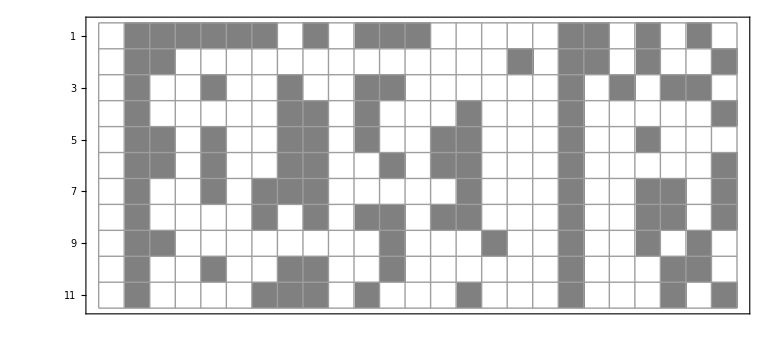

```mathematica
ArrayPlot[Values[simulation],ColorRules->{True->Gray,False->White},Mesh->True,Frame->True,FrameTicks->{{Range[1,n+1],None},{None,Thread[{Range@Length[F],Keys[F]}]}}]
```

The set of variables of the Boolean network.

```mathematica
Keys[TF]
```

{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}

#### Interaction graph

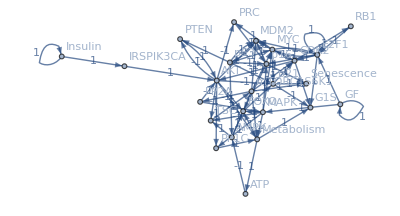

```mathematica
ig0 = InteractionGraphSimple[TF]
```

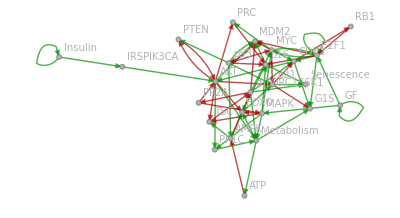

```mathematica
NiceIG[ig0]
```

```mathematica
NiceIG3D[ig0]
```

-Graphics3D-

#### Regulators

```mathematica
Regulators[ig0, mTORC1S6K1, {-1,0,1}]
```

{AMPK,TSC}

```mathematica
Regulators[ig0, Senescence, {-1,1}]
```

{mTORC1S6K1,p16,p21}

```mathematica
Regulators[ig0, G1S, {-1}]
```

{p21}

```mathematica
Regulators[ig0, G1S, {1}]
```

{CDK2,E2F1,Metabolism}

#### State graph computation

The computation of a model (state graph)  depends on the modalities. Two modalities are predefined

Sequential and Parallel modes.

```mathematica
sequential=Sequential@Keys[TF]
```

{{Insulin},{GF},{Senescence},{G1S},{MAPK},{p16},{MDM2},{p53},{p21},{AKT},{mTORC1S6K1},{ATP},{IRSPIK3CA},{AMPK},{PTEN},{TSC},{MYC},{CDK2},{RB1},{E2F1},{PRC},{Metabolism},{PP2A},{FOXO},{PP1C}}

```mathematica
parall=Parallel@Keys[TF]
```

{{Insulin,GF,Senescence,G1S,MAPK,p16,MDM2,p53,p21,AKT,mTORC1S6K1,ATP,IRSPIK3CA,AMPK,PTEN,TSC,MYC,CDK2,RB1,E2F1,PRC,Metabolism,PP2A,FOXO,PP1C}}

Sequential vs. Asynchronous is by  default.

sg = ModelOf[F]

ModelOf[F]

NiceModel[sg, EdgeLabels -> Automatic]

NiceModel[ModelOf[F], EdgeLabels -> Automatic]